```mathematica
SetDirectory["~/w2013/stat245"]
```

/home/hall/w2013/stat245

```mathematica
sz=Import["scripts_5/11_44/data_11_44ab_sz","List"]
```

{0.55,1.22,0.6,1.54,0.21,0.97,0.09,0.45,1.01,1.54,0.24,0.75,0.37,1.12,1.01,1.31,0.26,0.92,0.3,1.27,0.26,1.08,0.1,1.19,0.42,0.64,0.11,0.3,0.14,0.24,0.2,0.89,0.09,0.24,0.32,1.68,0.24,0.99,0.25,0.67}

```mathematica
sz0h=Take[sz,{1,40,2}]
```

{0.55,0.6,0.21,0.09,1.01,0.24,0.37,1.01,0.26,0.3,0.26,0.1,0.42,0.11,0.14,0.2,0.09,0.32,0.24,0.25}

```mathematica
sz2h=Take[sz,{2,40,2}]
```

{1.22,1.54,0.97,0.45,1.54,0.75,1.12,1.31,0.92,1.27,1.08,1.19,0.64,0.3,0.24,0.89,0.24,1.68,0.99,0.67}

```mathematica
nsz=Import["scripts_5/11_44/data_11_44ab_norm","List"]
```

{1.27,2.,0.09,0.41,1.64,2.37,0.23,0.41,0.18,0.79,0.12,0.94,0.85,1.72,0.69,1.75,0.78,1.6,0.63,1.8,0.5,2.08,0.62,1.58,0.19,0.86,0.66,1.92,0.91,1.54}

```mathematica
n0h=Take[nsz,{1,30,2}]
```

{1.27,0.09,1.64,0.23,0.18,0.12,0.85,0.69,0.78,0.63,0.5,0.62,0.19,0.66,0.91}

```mathematica
n2h=Take[nsz,{2,30,2}]
```

{2.,0.41,2.37,0.41,0.79,0.94,1.72,1.75,1.6,1.8,2.08,1.58,0.86,1.92,1.54}

```mathematica
nd=n2h-n0h
```

{0.73,0.32,0.73,0.18,0.61,0.82,0.87,1.06,0.82,1.17,1.58,0.96,0.67,1.26,0.63}

```mathematica
szd=sz2h-sz0h
```

{0.67,0.94,0.76,0.36,0.53,0.51,0.75,0.3,0.66,0.97,0.82,1.09,0.22,0.19,0.1,0.69,0.15,1.36,0.75,0.42}

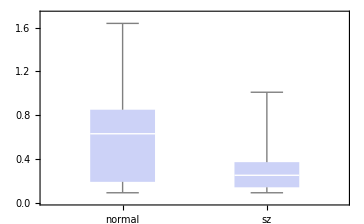

```mathematica
BoxWhiskerChart[{n0h,sz0h},ChartLabels->{"normal","sz"}]
```

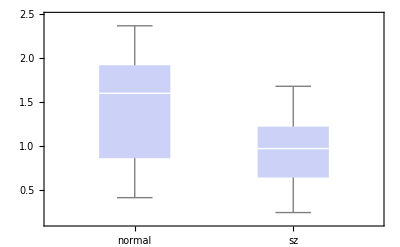

```mathematica
BoxWhiskerChart[{n2h,sz2h},ChartLabels->{"normal","sz"}]
```

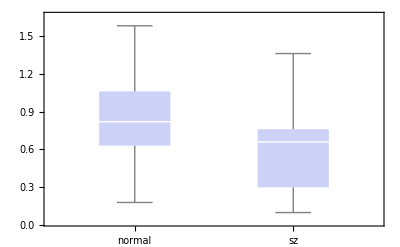

```mathematica
BoxWhiskerChart[{nd,szd},ChartLabels->{"normal","sz"}]
```

```mathematica
StandardDeviation[n0h]
```

0.439786

```mathematica
StandardDeviation[sz0h]
```

0.268686

```mathematica
TTest[{n0h,sz0h},0,"TestStatistic"]
```

TTest::nortst: At least one of the p-values in {0.430772, 0.0159244}, resulting from a test for normality, is below 0.025. The tests in {"T"} require that the data is normally distributed.

2.37734

```mathematica
makeTStat[x_,y_]:=(Mean[x]-Mean[y])/Sqrt[Variance[x]/Length[x]+Variance[y]/Length[y]]
```

```mathematica
makeDof[x_,y_]:=(Variance[x]/Length[x]+Variance[y]/Length[y])^2/((Variance[x]/Length[x])^2/(Length[x]-1)+(Variance[y]/Length[y])^2/(Length[y]-1))
```

```mathematica
Needs["HypothesisTesting`"]
```

```mathematica
makeTStat[n0h,sz0h]
```

2.22236

```mathematica
makeDof[n0h,sz0h]
```

21.6835

```mathematica
StudentTPValue[2.222,22,TwoSided->True]
```

TwoSidedPValue→0.0368796

```mathematica
makeTStat[n2h,sz2h]
```

2.69317

```mathematica
makeDof[n2h,sz2h]
```

23.8358

```mathematica
StudentTPValue[2.693,24,TwoSided->True]
```

TwoSidedPValue→0.0127089

```mathematica
makeTStat[nd,szd]
```

1.81826

```mathematica
makeDof[nd,szd]
```

29.4977

```mathematica
StudentTPValue[1.818,29,TwoSided->True]
```

TwoSidedPValue→0.0794086